### R-Pentomino

```mathematica
frames = 
Table[
ArrayPlot[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{i}}, {-25, 35}, {-45, 45}}], Mesh->True,MeshStyle->Opacity[.1]], {i, 500}];
```

```mathematica
Export[NotebookDirectory[]<>"anim2.mp4", frames]
```

$Aborted

```mathematica
AnimationVideo[ArrayPlot[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{i}}, {-25, 35}, {-45, 45}}], Mesh->True,MeshStyle->Opacity[.1]], {i, 1, 500, 1}]
```

AnimationVideo::prpchg: Warning: the output frame rate changed from 100 to 12500001/125000.

### Gosper glider gun

```mathematica
AnimationVideo[ArrayPlot[CellularAutomaton["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0}, {{{i}}, {-10, 35}, {-10, 45}}], Mesh->True,MeshStyle->Opacity[.1]], {i, 1, 200, 1}]
```

### Some complicated recognizable animatiion

```mathematica
Union[Values[#Class&/@ $LifeData]]
```

{Agar,Breeder,Caber tosser,Conduit,Constellation,Crawler,Eater,Fuse,Growing spaceship,Gun,Induction coil,Memory cell,Methuselah,Oscillator,Problem,Pseudo still life,Puffer,Reflector,Rotor,Sawtooth,Spacefiller,Spaceship,Spark,Still life component,Strict still life,Superstring,Unit cell,Wave,Wick,Wickstretcher}

```mathematica
Select[$LifeData, #Class === "Crawler"&]
```

<|(13,1)c/31 Pseudo-B climber→<|Name→(13,1)c/31 Pseudo-B climber,Year→2003,Class→Crawler,Speed→{13/31,1/31},Wiki→https://conwaylife.com/wiki/(13,1)c/31_Pseudo-B_climber,DataFiles→{131c31climber.rle},MatrixData→SparseArray[…],InitialWeight→60|>,(23,5)c/79 Herschel climber→<|Name→(23,5)c/79 Herschel climber,Year→2006,Class→Crawler,Speed→{23/79,5/79},Wiki→https://conwaylife.com/wiki/(23,5)c/79_Herschel_climber,DataFiles→{235c79climber.cells,235c79climber.rle},MatrixData→SparseArray[…],InitialWeight→55|>,31c/240 Herschel-pair climber→<|Name→31c/240 Herschel-pair climber,Year→2013,Class→Crawler,Speed→31/240,Wiki→https://conwaylife.com/wiki/31c/240_Herschel-pair_climber,DataFiles→{31c240reaction.cells,31c240reaction.rle},MatrixData→SparseArray[…],InitialWeight→11|>,(34,7)c/156 Herschel climber→<|Name→(34,7)c/156 Herschel climber,Year→2013,Class→Crawler,Speed→{17/78,7/156},Wiki→https://conwaylife.com/wiki/(34,7)c/156_Herschel_climber,DataFiles→{347c156climber.rle},MatrixData→SparseArray[…],InitialWeight→44|>,c/12 R-pentomino crawler→<|Name→c/12 R-pentomino crawler,Year→2014,Class→Crawler,Speed→1/12,Wiki→https://conwaylife.com/wiki/C/12_R-pentomino_crawler,DataFiles→{c12rpentominocrawler.cells,c12rpentominocrawler.rle},MatrixData→SparseArray[…],InitialWeight→39|>,(27,1)c/72 Herschel climber→<|Name→(27,1)c/72 Herschel climber,Year→2016,Class→Crawler,Speed→{3/8,1/72},Wiki→https://conwaylife.com/wiki/(27,1)c/72_Herschel_climber,DataFiles→{271c72climber.rle},MatrixData→SparseArray[…],InitialWeight→108|>|>

```mathematica
AnimationVideo[ArrayPlot[CellularAutomaton["GameOfLife",{$LifeData["(23,5)c/79 Herschel climber"]["MatrixData"], 0}, {{{i}}, {-10, 35}, {-10, 45}}], Mesh->True,MeshStyle->Opacity[.1]], {i, 1, 30, 1}]
```

### Breeder

```mathematica
Table[ArrayPlot[CellularAutomaton["GameOfLife",{$LifeData["Breeder 1"]["MatrixData"], 0}, {{{i}}, {0, 400}, {-100, 800}}], Mesh->False,MeshStyle->Opacity[.05]], {i, 1, 30, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Crawler

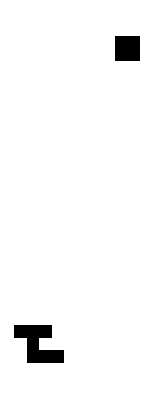

```mathematica
ArrayPlot[Normal[$LifeData["31c/240 Herschel-pair climber"]["MatrixData"]]]
```

```mathematica
Position[CellularAutomaton["GameOfLife",{$LifeData["31c/240 Herschel-pair climber"]["MatrixData"], 0}, {{{i}}, {-1000, 1000}, {-1000, 1000}}]]
```

```mathematica
AnimationVideo[ArrayPlot[CellularAutomaton["GameOfLife",{$LifeData["31c/240 Herschel-pair climber"]["MatrixData"], 0}, {{{i}}, {-50, 50}, {-50, 50}}], Mesh->False,MeshStyle->Opacity[.05]], {i, 1, 200, 1}]
```

#### Progressive Decrease for Constant Period (From WN-03)

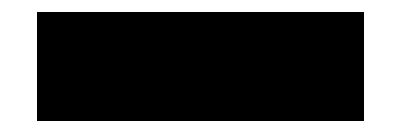
{-Graphics-{1969,2}
-Graphics-{1969,2},-Graphics-{1970,3}
-Graphics-{1989,3},-Graphics-{1970,4}
-Graphics-{1973,4},-Graphics-{1971,5}
-Graphics-{1994,5},-Graphics-{1972,6}
-Graphics-{1976,6},-Graphics-{1972,7}
-Graphics-{1972,7},-Graphics-{1970,8}
-Graphics-{1970,8},-Graphics-{1972,9}
-Graphics-{1997,9},-Graphics-{1983,10}
-Graphics-{2010,10},-Graphics-{1977,11}
-Graphics-{2016,11},-Graphics-{1972,12}
-Graphics-{2023,12},-Graphics-{1976,13}
-Graphics-{2009,13},-Graphics-{1970,14}
-Graphics-{1970,14},-Graphics-{1970,15}
-Graphics-{1970,15},-Graphics-{1983,16}
-Graphics-{2020,16},-Graphics-{1997,17}
-Graphics-{2014,17},-Graphics-{1995,18}
-Graphics-{1995,18},-Graphics-{2023,19}
-Graphics-{2023,19},-Graphics-{1995,20}
-Graphics-{2022,20},-Graphics-{1995,21}
-Graphics-{2022,21},-Graphics-{1997,22}
-Graphics-{2000,22},-Graphics-{2019,23}
-Graphics-{2022,23},-Graphics-{1994,24}
-Graphics-{2002,24},-Graphics-{1994,25}
-Graphics-{2022,25},-Graphics-{1983,26}
-Graphics-{2023,26},-Graphics-{2002,27}
-Graphics-{2010,27},-Graphics-{1973,28}
-Graphics-{2016,28},-Graphics-{1980,29}
-Graphics-{1980,29},-Graphics-{1970,30}
-Graphics-{1970,30},-Graphics-{2010,31}
-Graphics-{2010,31},-Graphics-{1978,32}
-Graphics-{2021,32},-Graphics-{1997,33}
-Graphics-{2000,33},-Graphics-{2022,34}
-Graphics-{2022,34},-Graphics-{1995,35}
-Graphics-{2016,35},-Graphics-{1984,36}
-Graphics-{1995,36},-Graphics-{2009,37}
-Graphics-{2022,37},-Graphics-{2022,38}
-Graphics-{2023,38},-Graphics-{2000,39}
-Graphics-{2022,39},-Graphics-{1994,40}
-Graphics-{2009,40},-Graphics-{2023,41}
-Graphics-{2023,41},-Graphics-{1994,42}
-Graphics-{1994,42},-Graphics-{2013,43}
-Graphics-{2022,43},-Graphics-{1992,44}
-Graphics-{2022,44},-Graphics-{2022,45}
-Graphics-{2022,45},-Graphics-{1971,46}
-Graphics-{1971,46},-Graphics-{1982,47}
-Graphics-{1982,47},-Graphics-{1994,48}
-Graphics-{2022,48},-Graphics-{1999,49}
-Graphics-{2023,49},-Graphics-{1992,50}
-Graphics-{1994,50},-Graphics-{2009,51}
-Graphics-{2022,51},-Graphics-{1977,52}
-Graphics-{1977,52},-Graphics-{2023,53}
-Graphics-{2023,53},-Graphics-{1973,54}
-Graphics-{2022,54},-Graphics-{1986,55}
-Graphics-{2012,55},-Graphics-{2022,56}
-Graphics-{2024,56},-Graphics-{1997,57}
-Graphics-{2022,57},-Graphics-{1994,58}
-Graphics-{2022,58},-Graphics-{1997,59}
-Graphics-{2023,59},-Graphics-{1971,60}
-Graphics-{1971,60},-Graphics-{1996,61}
-Graphics-{2022,61},-Graphics-{2010,62}
-Graphics-{2021,62},-Graphics-{2023,63}
-Graphics-{2023,63},-Graphics-{2010,64}
-Graphics-{2010,64},-Graphics-{2021,65}
-Graphics-{2023,65},-Graphics-{2023,66}
-Graphics-{2023,66},-Graphics-{1996,67}
-Graphics-{2013,67},-Graphics-{2022,68}
-Graphics-{2023,68},-Graphics-{2023,69}
-Graphics-{2023,69},-Graphics-{2007,70}
-Graphics-{2007,70},-Graphics-{2022,71}
-Graphics-{2022,71},-Graphics-{1990,72}
-Graphics-{1990,72},-Graphics-{2022,73}
-Graphics-{2022,73},-Graphics-{2021,74}
-Graphics-{2021,74},-Graphics-{1984,75}
-Graphics-{1984,75},-Graphics-{2021,76}
-Graphics-{2023,76},-Graphics-{2022,77}
-Graphics-{2022,77},-Graphics-{2023,78}
-Graphics-{2023,78},-Graphics-{1996,79}
-Graphics-{2022,79},-Graphics-{2018,80}
-Graphics-{2023,80},-Graphics-{2022,81}
-Graphics-{2022,81},-Graphics-{2022,82}
-Graphics-{2023,82},-Graphics-{2022,83}
-Graphics-{2022,83},-Graphics-{2007,84}
-Graphics-{2022,84},-Graphics-{2019,85}
-Graphics-{2022,85},-Graphics-{2022,86}
-Graphics-{2022,86},-Graphics-{2016,87}
-Graphics-{2016,87},-Graphics-{1996,88}
-Graphics-{1996,88},-Graphics-{1998,90}
-Graphics-{2023,90},-Graphics-{2022,91}
-Graphics-{2023,91},-Graphics-{1994,92}
-Graphics-{2022,92},-Graphics-{2023,93}
-Graphics-{2023,93},-Graphics-{2022,94}
-Graphics-{2022,94},-Graphics-{2022,95}
-Graphics-{2022,95},-Graphics-{2021,96}
-Graphics-{2021,96},-Graphics-{2023,97}
-Graphics-{2023,97},-Graphics-{2021,98}
-Graphics-{2021,98},-Graphics-{1994,100}
-Graphics-{2022,100},-Graphics-{2023,101}
-Graphics-{2023,101},-Graphics-{2022,102}
-Graphics-{2022,102},-Graphics-{2022,104}
-Graphics-{2022,104},-Graphics-{2023,105}
-Graphics-{2023,105},-Graphics-{2022,106}
-Graphics-{2022,106},-Graphics-{2023,107}
-Graphics-{2023,107},-Graphics-{2022,108}
-Graphics-{2022,108},-Graphics-{2022,109}
-Graphics-{2022,109},-Graphics-{1994,110}
-Graphics-{2023,110},-Graphics-{2022,111}
-Graphics-{2022,111},-Graphics-{2022,112}
-Graphics-{2022,112},-Graphics-{2021,113}
-Graphics-{2021,113},-Graphics-{2015,114}
-Graphics-{2015,114},-Graphics-{2023,115}
-Graphics-{2023,115},-Graphics-{2023,117}
-Graphics-{2023,117},-Graphics-{2024,118}
-Graphics-{2024,118},-Graphics-{2023,119}
-Graphics-{2023,119},-Graphics-{2022,120}
-Graphics-{2022,120},-Graphics-{2023,121}
-Graphics-{2023,121},-Graphics-{2022,122}
-Graphics-{2022,122},-Graphics-{1994,124}
-Graphics-{1994,124},-Graphics-{2023,125}
-Graphics-{2023,125},-Graphics-{2023,126}
-Graphics-{2023,126},-Graphics-{2022,127}
-Graphics-{2022,127},-Graphics-{2021,128}
-Graphics-{2023,128},-Graphics-{1993,129}
-Graphics-{2022,129},-Graphics-{2001,130}
-Graphics-{2001,130},-Graphics-{2022,132}
-Graphics-{2023,132},-Graphics-{1989,135}
-Graphics-{1989,135},-Graphics-{2023,136}
-Graphics-{2023,136},-Graphics-{2002,138}
-Graphics-{2002,138},-Graphics-{2023,139}
-Graphics-{2023,139},-Graphics-{2022,140}
-Graphics-{2023,140},-Graphics-{2020,143}
-Graphics-{2020,143},-Graphics-{1994,144}
-Graphics-{1994,144},-Graphics-{2022,146}
-Graphics-{2022,146},-Graphics-{2021,147}
-Graphics-{2022,147},-Graphics-{2023,148}
-Graphics-{2023,148},-Graphics-{2022,150}
-Graphics-{2023,150},-Graphics-{1975,156}
-Graphics-{1995,156},-Graphics-{2023,158}
-Graphics-{2023,158},-Graphics-{2023,159}
-Graphics-{2023,159},-Graphics-{2022,160}
-Graphics-{2022,160},-Graphics-{2023,164}
-Graphics-{2023,164},-Graphics-{1989,165}
-Graphics-{1989,165},-Graphics-{2022,166}
-Graphics-{2022,166},-Graphics-{1995,168}
-Graphics-{1995,168},-Graphics-{2023,174}
-Graphics-{2023,174},-Graphics-{2023,175}
-Graphics-{2023,175},-Graphics-{2022,176}
-Graphics-{2022,176},-Graphics-{2007,177}
-Graphics-{2007,177},-Graphics-{2021,182}
-Graphics-{2021,182},-Graphics-{2022,184}
-Graphics-{2022,184},-Graphics-{2022,186}
-Graphics-{2022,186},-Graphics-{2022,192}
-Graphics-{2022,192},-Graphics-{2021,196}
-Graphics-{2021,196},-Graphics-{2022,199}
-Graphics-{2022,199},-Graphics-{1994,200}
-Graphics-{1994,200},-Graphics-{2023,201}
-Graphics-{2023,201},-Graphics-{2021,217}
-Graphics-{2021,217},-Graphics-{2022,220}
-Graphics-{2022,220},-Graphics-{2023,224}
-Graphics-{2023,224},-Graphics-{2022,253}
-Graphics-{2022,253},-Graphics-{2023,280}
-Graphics-{2023,280},-Graphics-{2023,384}
-Graphics-{2023,384},-Graphics-{2022,444}
-Graphics-{2022,444},-Graphics-{2021,486}
-Graphics-{2021,486},-Graphics-{2021,576}
-Graphics-{2021,576},-Graphics-{1990,2700}
-Graphics-{1990,2700},-Graphics-{1992,15240}
-Graphics-{1992,15240},-Graphics-{1995,40894}
-Graphics-{1995,40894}}

```mathematica
Column/@Transpose[Table[Map[Labeled[ArrayPlot[#MatrixData,ImageSize->20 Sqrt[Dimensions[#MatrixData]]],{#Year,#Period}]&,SortBy[First/@Map[MinimalBy[#,#[tt]&]&,Values@GroupBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period&]],#Period&]],{tt,{"Year","InitialWeight"}}]]
```

```mathematica
weightsovertime = SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == 3&], #Year&][[All, "InitialWeight"]]
```

{18,48,28,54,18,30,33,144,14,26,26,40,40,45,31,22,40,32,36,46,18,18,60,16,22,13,16,12,28,65,16,16,70,48,29,48,144,60,24,190,258,19,140,21,33,33,30}

```mathematica
improvements = FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime]
```

{∞,18,18,18,18,18,18,18,18,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12}

```mathematica
locs = Select[Partition[improvements, 2, 1],#[[1]] != #[[2]]&-> "Index"]
```

{1,9,26,28}

```mathematica
ArrayPlot[#MatrixData, ImageSize->6Last[Dimensions[#MatrixData]], Mesh->True]&/@ SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == 3&], #Year&][[locs]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

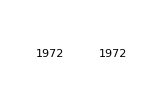
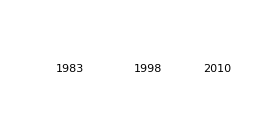
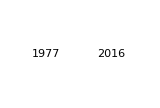
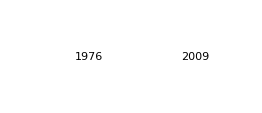
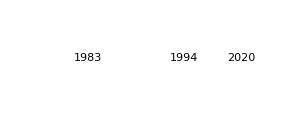
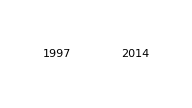
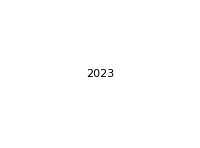
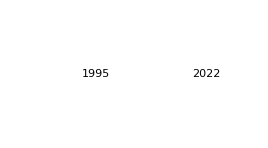
-Graphics-Period: 1
-Graphics-Period: 2
-Graphics-Period: 3
-Graphics-Period: 4
-Graphics-Period: 5
-Graphics-Period: 6
-Graphics-Period: 7
-Graphics-Period: 8
-Graphics-Period: 9
-Graphics-Period: 10
-Graphics-Period: 11
-Graphics-Period: 12
-Graphics-Period: 13
-Graphics-Period: 14
-Graphics-Period: 15
-Graphics-Period: 16
-Graphics-Period: 17
-Graphics-Period: 18
-Graphics-Period: 19
-Graphics-Period: 20

```mathematica
Column[Table[
Module[{weightsovertime, improvements, locs, p = i},
weightsovertime = SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&][[All, "InitialWeight"]];
improvements = FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime];
locs = Select[Partition[improvements, 2, 1],#[[1]] != #[[2]]&-> "Index"];Labeled[GraphicsRow[Labeled[ArrayPlot[#MatrixData, ImageSize->6Last[Dimensions[#MatrixData]], Mesh->True], #Year]&/@ SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&][[locs]]], "Period: "<> ToString[i], Left]
], {i, 1,20}]]
```

By bounding box

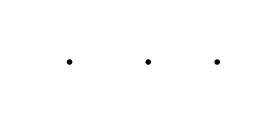
-Graphics-Period: 1
-Graphics-Period: 2
-Graphics-Period: 3
-Graphics-Period: 4
-Graphics-Period: 5
-Graphics-Period: 6
-Graphics-Period: 7
-Graphics-Period: 8
-Graphics-Period: 9
-Graphics-Period: 10
-Graphics-Period: 11
-Graphics-Period: 12
-Graphics-Period: 13
-Graphics-Period: 14
-Graphics-Period: 15
-Graphics-Period: 16
-Graphics-Period: 17
-Graphics-Period: 18
-Graphics-Period: 19
-Graphics-Period: 20

```mathematica
Column[Table[
Module[{weightsovertime, improvements, locs, p = i},
weightsovertime = 
Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&];
improvements = FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime];
locs = Select[Partition[improvements, 2, 1],#[[1]] != #[[2]]&-> "Index"];Labeled[GraphicsRow[ArrayPlot[#MatrixData, ImageSize->6Last[Dimensions[#MatrixData]], Mesh->True]&/@ SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&][[locs]]], "Period: "<> ToString[i], Left]
], {i, 1,20}]]
```

```mathematica
Module[{weightsovertime, improvements, locs, p = 28},
weightsovertime = 
Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&];
improvements = FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime];
locs = Select[Partition[improvements, 2, 1],#[[1]] != #[[2]]&-> "Index"];#Name&/@ SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&][[locs]]]
```

{Newshuttle,Karel's p28,p28 pre-pulsar shuttle}

```mathematica
Module[{weightsovertime, improvements, locs, p = 16},
weightsovertime = 
Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&];
improvements = FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime];
locs = Select[Partition[improvements, 2, 1],#[[1]] != #[[2]]&-> "Index"];#Name&/@ SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&][[locs]]]
```

{Two pre-L hasslers,Achim's p16,Rich's p16,Rob's p16}

```mathematica
Module[{weightsovertime, improvements, locs, p = 16},
weightsovertime = 
Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&];
improvements = FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime];
locs = Select[Partition[improvements, 2, 1],#[[1]] != #[[2]]&-> "Index"];#Name&/@ SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&][[locs]]]
```

Why isn’t trails showing up?

```mathematica
GraphicsGrid[CellularAutomatonCompositePlot[#,{"Static"->50,{"Trails",10,.9}->40,{"3D",6}->30},1]&/@{"Beehive","Block","Loaf"},Dividers->{False,All},FrameStyle->Opacity[.3]]
```

-Graphics-

```mathematica
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == p&], #Year&]
```

{}